```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample/EXTRA_UPSAMPLE"];
meamFiles4={"TI_EpotminusEperf_all2_EXTRA_4_2500","TI_EpotminusEperf_all_EXTRA_4_2500"};
dftUPFiles4={"TI_UP_E0all_EXTRA_4_2500","TI_UP_Fall_EXTRA_4_2500"};
meamData4=Table[ReadList[meamFiles4[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,2}];
dftUPData4=Table[ReadList[dftUPFiles4[[i]],{Number}],{i,1,2}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols=N[{4.685,4.730,4.759,4.801,4.850},3];
eVcel2meVatom=1000/64;
```

```mathematica
Length[meamData4[[2]]]/5
dft4[[1]]//Length
```

101

101

```mathematica
Transpose[meamData4[[2]]][[5]]//Length
```

505

```mathematica
meam4=Partition[Transpose[meamData4[[2]]][[5]],Length[meamData4[[2]]]/5];
dft4=eVcel2meVatom*Table[Partition[Transpose[dftUPData4[[1]]][[1]],Length[meamData4[[2]]]/5][[i]]-Partition[Transpose[dftUPData4[[1]]][[1]],Length[meamData4[[2]]]/5][[i]][[1]],{i,1,5}];
dftf4=eVcel2meVatom*Table[Partition[Transpose[dftUPData4[[2]]][[1]],Length[meamData4[[2]]]/5][[i]]-Partition[Transpose[dftUPData4[[2]]][[1]],Length[meamData4[[2]]]/5][[i]][[1]],{i,1,5}];
```

```mathematica
(*Energy MVT TI UP-sample*)
GraphicsGrid[{{ListLinePlot[Table[(dft4-meam4)[[i]],{i,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample (meV/atom)"},ImageSize->600],ListPlot[Table[Table[Mean[(dft4-meam4)[[j]][[1;;i]]],{i,1,Length[meamData4[[2]]]/5}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample mean\n (meV/atom)"},ImageSize->600],ListPlot[Table[Table[StandardDeviation[(dft4-meam4)[[j]][[1;;i]]/Sqrt[i]],{i,2,Length[meamData4[[2]]]/5}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\n UP-samples","UP-sample uncertainty\n (meV/atom)"},PlotRange->All,ImageSize->600]}},ImageSize->2050]
Table[{Mean[(dft4-meam4)[[i]]],StandardDeviation[(dft4-meam4)[[i]]],StandardDeviation[(dft4-meam4)[[i]]]/Sqrt[Length[(dft4-meam4)[[i]]]]},{i,1,5}]//TableForm
```

-Graphics-

13.0405 | 3.19963 | 0.318375
7.27976 | 3.27155 | 0.325531
2.69994 | 2.89905 | 0.288466
-0.673546 | 3.58647 | 0.356868
-5.60963 | 3.44933 | 0.343221

```mathematica
edist4=Table[EstimatedDistribution[(dft4-meam4)[[i]],SkewNormalDistribution[μ,σ,alpha]],{i,1,5}];
edist4//TableForm
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

SkewNormalDistribution[19.9662,7.62219,-3638.37]
SkewNormalDistribution[4.89324,4.0364,1.10859]
SkewNormalDistribution[4.50825,3.4046,-0.891858]
SkewNormalDistribution[-3.65724,4.65166,1.34747]
SkewNormalDistribution[-3.11612,4.24236,-1.08346]

NormalDistribution[13.0405,3.18375]
NormalDistribution[7.27976,3.25531]
NormalDistribution[2.69994,2.88466]
NormalDistribution[-0.673546,3.56868]
NormalDistribution[-5.60963,3.43221]

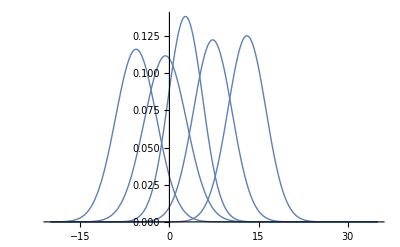

```mathematica
edistn4=Table[EstimatedDistribution[(dft4-meam4)[[i]],NormalDistribution[μ,σ]],{i,1,5}]//TableForm
```

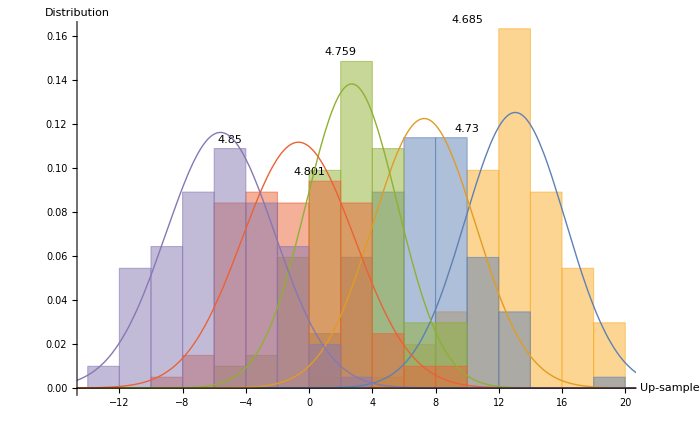

```mathematica
ldata4=Table[Labeled[(dft4-meam4)[[i]],vols[[i]],Above],{i,1,5}];
Show[Histogram[ldata4,20,"PDF",AxesLabel->{"Up-sample","Distribution"}],Plot[Evaluate@Table[PDF[edistn4[[1]][[i]],x],{i,1,5}],{x,-20,35},PlotStyle->Thick],ImageSize->700]
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
andyFah=Partition[Transpose[ReadList["Fah_surface_andy_tu-tild",{Number,Number,Number,Number}]][[3]],5];
MVTintAll=Transpose@ReadList["MVT_intall",{Number, Number,Number,Number,Number}];
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
```

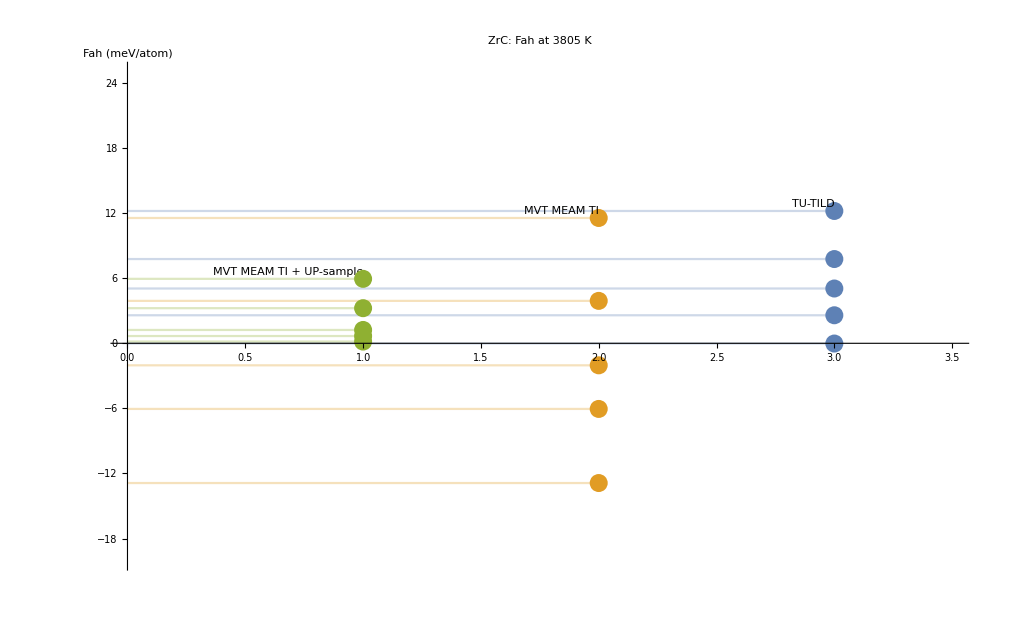

```mathematica
horizontalListPlotFill@ListPlot[{Labeled[Transpose@{Table[3,{i,1,5}],Transpose[andyFah][[3]]},"TU-TILD",Above],Labeled[Transpose@{Table[2,{i,1,5}],Transpose[MVTintAll][[3]]},"MVT MEAM TI",Above],Labeled[Transpose@{Table[1,{i,1,5}],Transpose[MVTintAll][[3]]+Table[Mean[(dft4-meam4)[[i]]],{i,1,5}]},"MVT MEAM TI + UP-sample",Above]},PlotLegends->SwatchLegend["TU-TILD","MVT MEAM TI","MVT MEAM TI + UPsample"],PlotRange->{{0,3.5},{-20,25}},PlotLabel->"ZrC: Fah at 3805 K",AxesLabel->{"","Fah (meV/atom)"},Ticks->{None,Automatic}]
```

```mathematica
Transpose[andyFah][[4]]
```

{-0.172075,2.71939,5.65059,10.2369,18.7489}

```mathematica
Table[Mean[(dft5-meam5)[[i]]],{i,1,5}]
Table[Mean[(dftf5-meam5)[[i]]],{i,1,5}]
Transpose[MVTintAll][[4]]+Table[Mean[(dft5-meam5)[[i]]],{i,1,5}]
```

{15.1432,7.88656,2.65205,-1.45456,-5.38734}

{8.4332,1.16119,-4.17762,-8.69369,-12.8361}

{0.323173,2.14656,1.55205,4.63544,11.0727}

```mathematica
Table[Mean[(dft4-meam4)[[i]]],{i,1,5}]
Table[Mean[(dftf4-meam4)[[i]]],{i,1,5}]
Transpose[MVTintAll][[3]]+Table[Mean[(dft4-meam4)[[i]]],{i,1,5}]
Transpose[andyFah][[3]]
```

{13.0405,7.27976,2.69994,-0.673546,-5.60963}

{10.5065,4.47355,-0.164112,-3.7488,-8.61324}

{0.160487,1.22976,0.66994,3.23645,5.94037}

{-0.0219889,2.58376,5.04972,7.76604,12.1956}